Unit step function

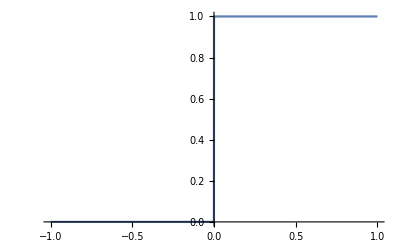

```mathematica
Plot[HeavisideTheta[x],{x,-1,1}]
```

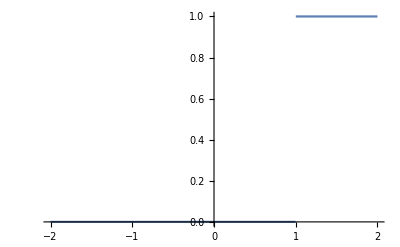

```mathematica
Plot[HeavisideTheta[x-1],{x,-2,2}]
```

```mathematica
Step1[x_]:=HeavisideTheta[x]-HeavisideTheta[x-1]
```

Graph unit step function

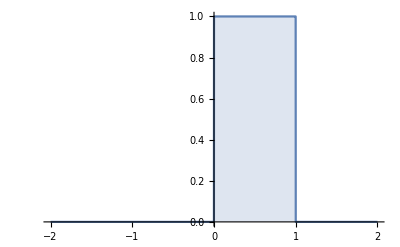

```mathematica
Plot[Step1[x],{x,-2,2}, Filling-> Bottom]
```

Unit step function with prescribed support interval

```mathematica
Step2[x_,a_,b_]:=Step1[(x-a)/(b-a)];
```

Example of graphs

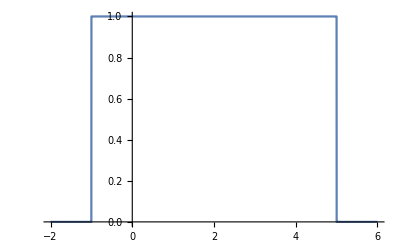

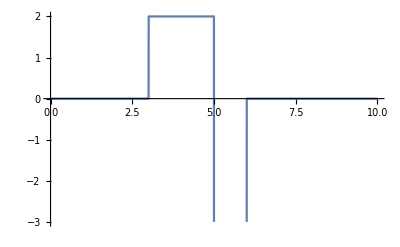

```mathematica
Plot[Step2[x,-1,5],{x,-2,6}]
Plot[2*Step2[x,3,5]-6*Step2[x,5,6],{x,0,10}]
```

```mathematica
Integrate[Floor[x/2],{x,1/2,10}]
```

20

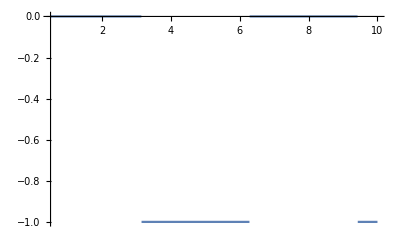

```mathematica
Plot[Floor[Sin[x]],{x,1/2,10}]
```

Homogeneous partition of  interval [a,b] with length n

```mathematica
HomogeneousP[a_,b_,n_]:=Table[a+(i)*((b-a)/n),{i,0,n}];
```

Example homogeneous partition

```mathematica
HomogeneousP[0,10,100]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10,21/5,43/10,22/5,9/2,23/5,47/10,24/5,49/10,5,51/10,26/5,53/10,27/5,11/2,28/5,57/10,29/5,59/10,6,61/10,31/5,63/10,32/5,13/2,33/5,67/10,34/5,69/10,7,71/10,36/5,73/10,37/5,15/2,38/5,77/10,39/5,79/10,8,81/10,41/5,83/10,42/5,17/2,43/5,87/10,44/5,89/10,9,91/10,46/5,93/10,47/5,19/2,48/5,97/10,49/5,99/10,10}

Choosing sampling point for heights in Riemann sum, given a partition P

```mathematica
LeftPoint[P_]:=Table[P[[i]],{i,1,Length[P]-1}];
RightPoint[P_]:=Table[P[[i+1]],{i,1,Length[P]-1}];
MidPoint[P_]:=Table[(P[[i]]+P[[i+1]])/2,{i,1,Length[P]-1}];
RandomPointSample[P_]:=Table[RandomPoint[Interval[{P[[i]],P[[i+1]]}]],{i,1,Length[P]-1}];
```

Examples of sampling points

```mathematica
P0=HomogeneousP[-2,15,30];
LeftPoint[P0]
RightPoint[P0]
MidPoint[P0]
RandomPointSample[P0]
```

{-2,-43/30,-13/15,-3/10,4/15,5/6,7/5,59/30,38/15,31/10,11/3,127/30,24/5,161/30,89/15,13/2,106/15,229/30,41/5,263/30,28/3,99/10,157/15,331/30,58/5,73/6,191/15,133/10,208/15,433/30}

{-43/30,-13/15,-3/10,4/15,5/6,7/5,59/30,38/15,31/10,11/3,127/30,24/5,161/30,89/15,13/2,106/15,229/30,41/5,263/30,28/3,99/10,157/15,331/30,58/5,73/6,191/15,133/10,208/15,433/30,15}

{-103/60,-23/20,-7/12,-1/60,11/20,67/60,101/60,9/4,169/60,203/60,79/20,271/60,61/12,113/20,373/60,407/60,147/20,95/12,509/60,181/20,577/60,611/60,43/4,679/60,713/60,249/20,781/60,163/12,283/20,883/60}

{{-1.8912},{-1.2014},{-0.790987},{0.257815},{0.796938},{1.02247},{1.92474},{2.49549},{2.83243},{3.40591},{3.89858},{4.6659},{5.26835},{5.43245},{6.32166},{6.51231},{7.40641},{7.76988},{8.44872},{9.12064},{9.34411},{10.099},{10.9727},{11.0421},{11.6028},{12.6092},{12.932},{13.4169},{14.0821},{14.9539}}

Función escalonada sobre partición homogenea P de longitud n con puntos muestra S dados por f

```mathematica
StepFunction2[f_,P_,S_]:=Sum[f[S[[i]]]Step2[x,P[[i]],P[[i+1]]],{i,1,Length[P]-1}];
```

Ejemplos de funciones escalonadas

```mathematica
f[x_]:=x^2;
```

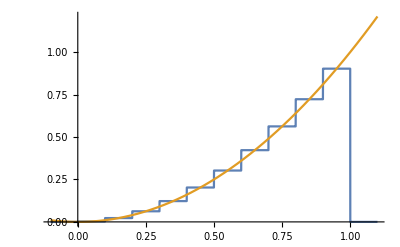

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,1,10],MidPoint[HomogeneousP[0,1,10]]],f[x]},{x,-0.1,1.1}]
```

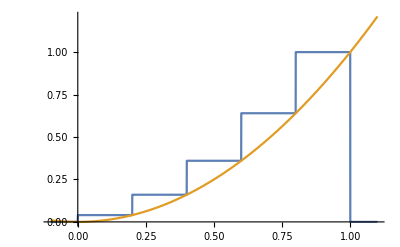

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,1,5],RightPoint[HomogeneousP[0,1,5]]],f[x]},{x,-0.1,1.1}]
```

```mathematica
HomogeneousP[0,Pi,20]
S=RandomPointSample[HomogeneousP[0,Pi,20]]
```

{0,π/20,π/10,(3 π)/20,π/5,π/4,(3 π)/10,(7 π)/20,(2 π)/5,(9 π)/20,π/2,(11 π)/20,(3 π)/5,(13 π)/20,(7 π)/10,(3 π)/4,(4 π)/5,(17 π)/20,(9 π)/10,(19 π)/20,π}

{{0.153698},{0.229951},{0.460736},{0.623435},{0.762434},{0.897426},{0.962044},{1.23175},{1.36571},{1.48059},{1.64873},{1.85654},{1.93903},{2.08354},{2.3373},{2.37939},{2.63814},{2.69607},{2.9296},{3.11531}}

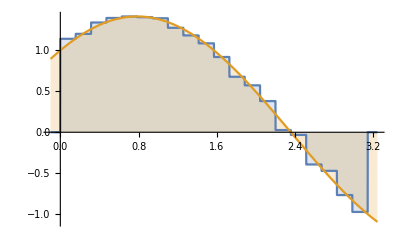

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,Pi,20],S],f[x]},{x,-0.1,Pi+0.1},Filling->Axis]
```

Problem with random sample, it seems there is a double loop, seprate computation for random sample works

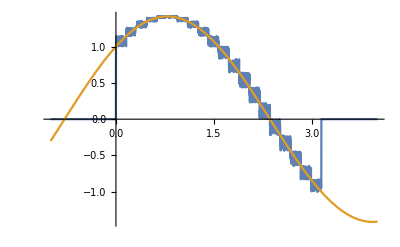

```mathematica
Plot[{StepFunction2[f,HomogeneousP[0,Pi,20],RandomPointSample[HomogeneousP[0,Pi,20]]],f[x]},{x,-1,4}]
```

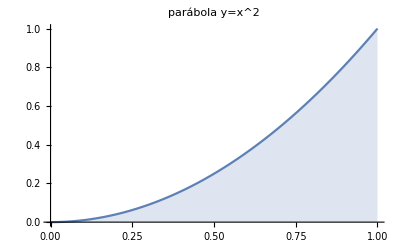

```mathematica
Plot[x^2,{x,0,1},Filling->Axis,PlotLabel->Style["parábola y=x^2",FontSize->15]]
```

```mathematica
f[x_]:=x^2;
line=Line[{1,0},{1,2}]
```

Line[{1,0},{1,2}]

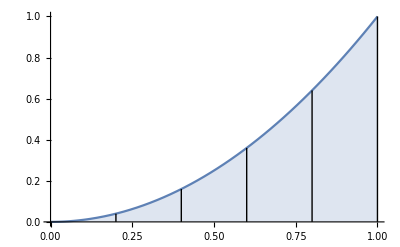

```mathematica
Plot[f[x],{x,0,1}, 
Epilog->
{Line[{{0.2,0},{0.2,(0.2)^2}}],
Line[{{0.4,0},{0.4,(0.4)^2}}],
    Line[{{0.6,0},{0.6,(0.6)^2}}],
Line[{{0.8,0},{0.8,(0.8)^2}}],
Line[{{1,0},{1,1}}]
},Filling->Axis]
```